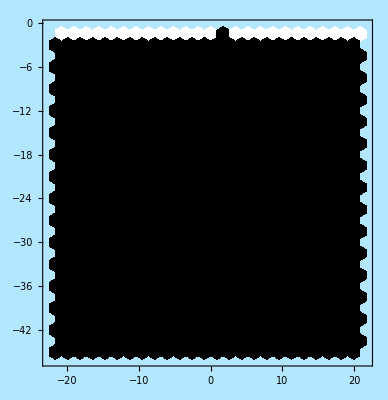
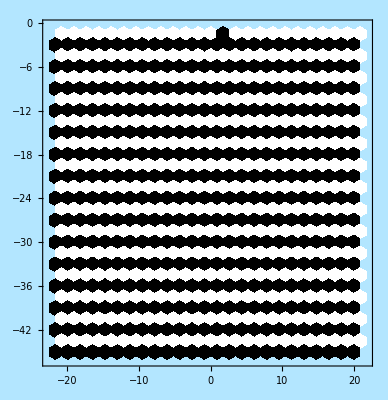
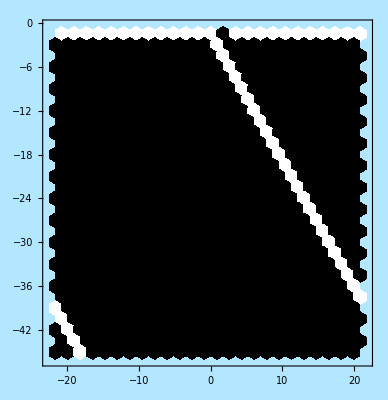
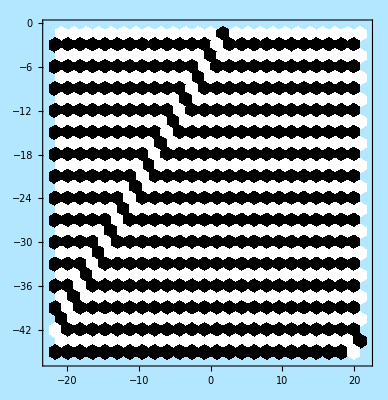
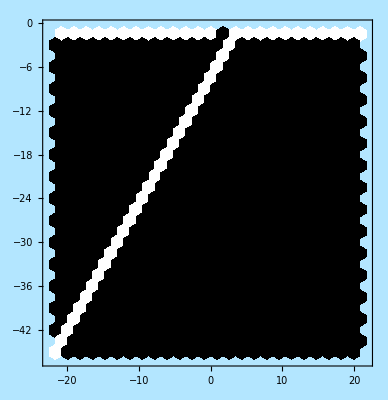
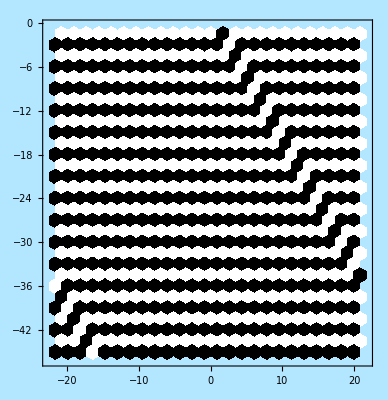
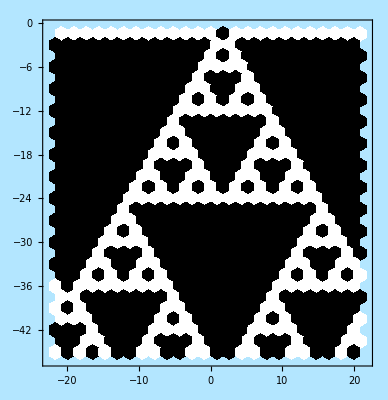
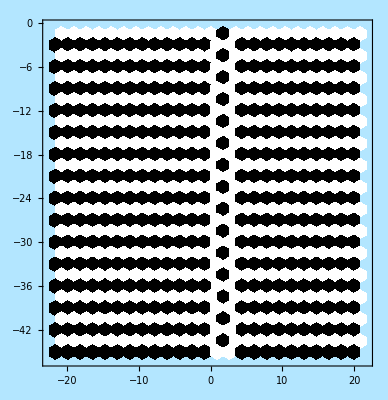
{-Graphics-
False,-Graphics-
NOR,-Graphics-
a AND not b,-Graphics-
NOT b,-Graphics-
not a AND b,-Graphics-
NOT a,-Graphics-
XOR,-Graphics-
NAND,-Graphics-
AND,-Graphics-
XNOR,-Graphics-
a,-Graphics-
a OR not b,-Graphics-
b,-Graphics-
not a OR b,-Graphics-
OR,-Graphics-
True}

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]

w = 25; h = 30;

arrs=(ReplacePart[Table[Table[0, {j, 1, h}, {i, 1, w}],{n,1,16}
][[#]],1->{1,1,1,1,1,1,1,1,1,1,1, 1, 0, 1,1,1,1,1,1,1,1,1,1,1,1}])&/@Range[16];

correctVec[{x_, y_}] := {1 + Mod[-1 + 9 w + x, w],1 + Mod[-1 + 9 h + y, h]}

neighborsVal[x_, y_,arr_] := (arr[[#[[2]]]][[#[[1]]]]) & /@ (correctVec[{x, y} + #]& /@ {{0, -1}, {1, -1}});

Table[Table[
  newArr = Table[
    Replace[neighborsVal[i, 
iterN,
arrs[[n]]], 
Dispatch[Table[
Table[{Mod[d,2],
Mod[Floor[d/2],2]}->Mod[Floor[(n-1)/(2^(d))],2],
{d,0,3}],
{n,1,16}
]][[n]]],
    {i, 1, w}
    ];
  arrs[[n]] = ReplacePart[arrs[[n]], iterN -> newArr];,{iterN, 2, h}],{n,1,16}];

pic[n_] := (
  theSideLength = 1;
  theHexRadius = (theSideLength/2)/Sin[2 π/(6*2)];
  theHexApothem = (theSideLength/2)/Tan[2 π/(6*2)];

   g = Flatten@Table[{If[arrs[[n]][[j]][[i]] > 0, White, Black],
RegularPolygon[{
 -(w)*theHexApothem + (Mod[i + j/2,w])*theHexApothem*2,
-j*(theSideLength-Sqrt[theSideLength^2 - theHexApothem^2])*3
},{theHexRadius, Pi/6}, 6]
      },{j, 1, h}, {i, 1, w}];

  Column[{Graphics[g, 
Background -> RGBColor[0.7, 0.9, 1], 
PlotRange -> {{-25, 25}, {2, -50}}, 
Frame -> True,
ImageSize->Tiny],
{"False","NOR","a AND not b","NOT b","not a AND b","NOT a","XOR","NAND","AND","XNOR","a","a OR not b","b","not a OR b","OR","True"}[[n]]}]
  )
pic/@Range[1,16]
```

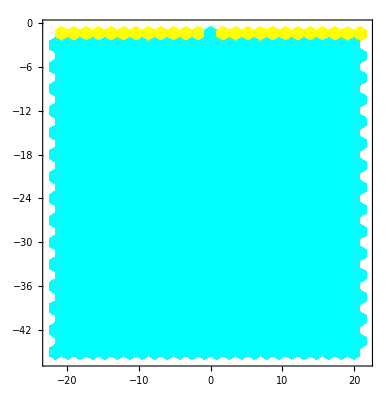
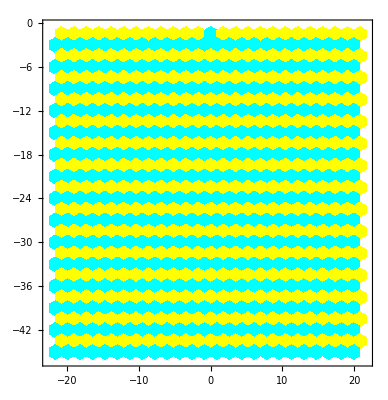
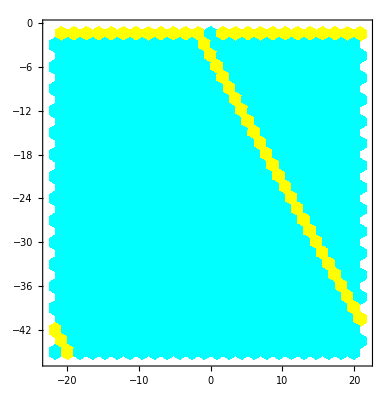
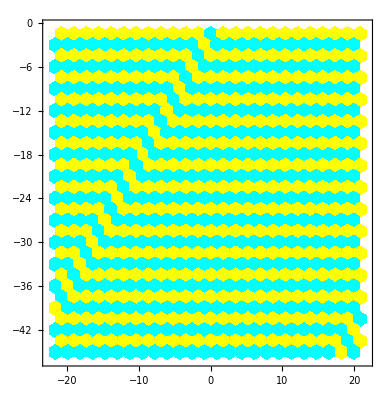
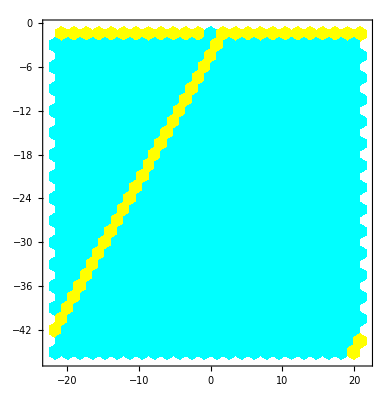
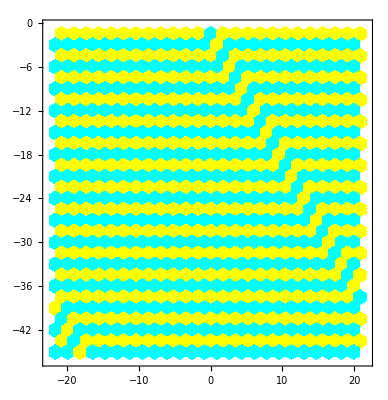
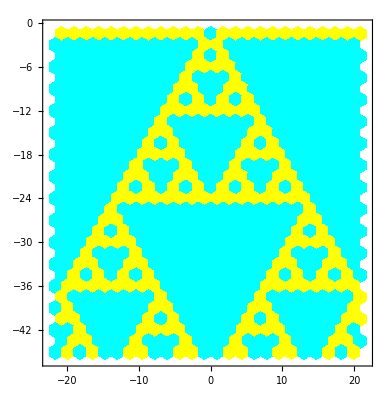
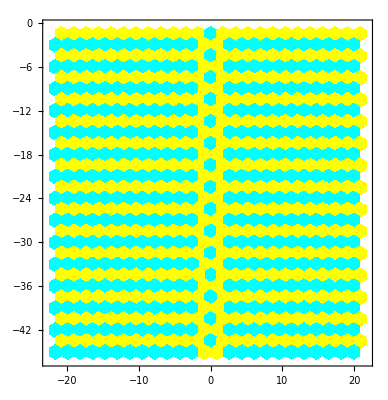
{-Graphics-
False,-Graphics-
NOR,-Graphics-
a AND not b,-Graphics-
NOT b,-Graphics-
not a AND b,-Graphics-
NOT a,-Graphics-
XOR,-Graphics-
NAND,-Graphics-
AND,-Graphics-
XNOR,-Graphics-
a,-Graphics-
a OR not b,-Graphics-
b,-Graphics-
not a OR b,-Graphics-
OR,-Graphics-
True}

```mathematica
w = 25; h = 30;

arrs=(ReplacePart[Table[Table[0, {j, 1, h}, {i, 1, w}],{n,1,16}][[#]],
1->{1,1,1,1,1,1,1,1,1,1,1, 0, 1, 1,1,1,1,1,1,1,1,1,1,1,1}])&/@Range[16];

correctVec[{x_, y_}] := {1 + Mod[-1 + 9 w + x, w],1 + Mod[-1 + 9 h + y, h]}

neighborsVal[x_, y_,arr_] := (arr[[#[[2]]]][[#[[1]]]]) & /@ (correctVec[{x, y} + #]& /@ {{0, -1}, {1, -1}});

Table[Table[
  newArr = Table[
    Replace[neighborsVal[i, 
iterN,
arrs[[n]]], 
Dispatch[Table[
Table[{Mod[d,2],
Mod[Floor[d/2],2]}->Mod[Floor[(n-1)/(2^(d))],2],
{d,0,3}],
{n,1,16}
]][[n]]],
    {i, 1, w}
    ];
  arrs[[n]] = ReplacePart[arrs[[n]], iterN -> newArr],{iterN, 2, h}],{n,1,16}];

pic[n_] := (
  theSideLength = 1;
  theHexRadius = (theSideLength/2)/Sin[2 π/(6*2)];
  theHexApothem = (theSideLength/2)/Tan[2 π/(6*2)];
   g = Flatten@Table[{If[arrs[[n]][[j]][[i]] > 0, RGBColor[100,71,0,66], Cyan],
RegularPolygon[{
 -(w)*theHexApothem + (Mod[i + j/2,w])*theHexApothem*2,
-j*(theSideLength-Sqrt[theSideLength^2 - theHexApothem^2])*3
},{theHexRadius, Pi/6}, 6]
      },{j, 1, h}, {i, 1, w}];
  Column[{Graphics[g,
PlotRange -> {{-25, 25}, {2, -50}}, 
Frame -> True,
ImageSize->Automatic],
{"False","NOR","a AND not b","NOT b","not a AND b","NOT a","XOR","NAND","AND","XNOR","a","a OR not b","b","not a OR b","OR","True"}[[n]]}]
  )
pic/@Range[1,16]
```

```mathematica
{{{-Graphics-}, {"False"}},{{-Graphics-}, {"NOR"}},{{-Graphics-}, {"a AND not b"}},{{-Graphics-}, {"NOT b"}},
{{-Graphics-}, {"not a AND b"}},{{-Graphics-}, {"NOT a"}},{{-Graphics-}, {"XOR"}},{{-Graphics-}, {"NAND"}},
{{-Graphics-}, {"AND"}},{{-Graphics-}, {"XNOR"}},{{-Graphics-}, {"a"}},{{-Graphics-}, {"a OR not b"}},
{{-Graphics-}, {"b"}},{{-Graphics-}, {"not a OR b"}},{{-Graphics-}, {"OR"}},{{-Graphics-}, {"True"}}}
```

```mathematica
RGBColor[0.1,0.1, 0.5]
```

RGBColor[0.1, 0.1, 0.5]

```mathematica
RGBColor[0.1,1,1]
```

RGBColor[0.1, 1, 1]

```mathematica
Darker[Blue]
```

RGBColor[0, 0, Rational[2, 3]]

```mathematica
Lighter[Cyan]
```

RGBColor[Rational[1, 3], 1, 1]

```mathematica
Cyan
```

RGBColor[0, 1, 1]

```mathematica
Blue
```

RGBColor[0, 0, 1]